# Polyhedral Gluing

If two polyhedra have a “compatible” face, meaning that the faces are the same polygon and have the same bilinear forms between each circle on the face, then a new polyhedron can be formed by gluing those two polyhedra together along that face. For example, two square pyramids can be glued along their square base resulting in an octahedron. Koebe-Andreev-Thurston then suggests that the same process can be done to packings. The gram matrix of the result can be computed in terms of the gram matrices of the two polyhedra being glued together, which is the point of this code.

## Code

fullGlue is the most useful function here. It takes two gram matrices and the number of vertices in the shared face. Importantly, the gram matrices should be organized so that the minor corresponding to the shared face is in the bottom left of the first gram matrix and top right of the second gram matrix.

```mathematica
glue[G_,n_,m_,p_]:=Block[{horizontal,vertical,eqs,solution,indices},
horizontal=Inverse[G⟦n-2;;n+1,n-2;;n+1⟧];
vertical=Inverse[G⟦n-p;;n-p+3,n-p;;n-p+3⟧];
eqs=Table[G⟦j,n+1+i⟧==horizontal.G⟦n-2;;n+1,n+1+i⟧.G⟦j,n-2;;n+1⟧,{i,m-1-p},{j,n-p}];
eqs=Flatten[AppendTo[eqs,Table[G⟦i,n+1+j⟧==vertical.G⟦i,n-p;;n-p+3⟧.G⟦n-p;;n-p+3,n+1+j⟧,{i,n-p},{j,m-1-p}]]];
indices=Join[{1},Range[n-p+1,n-p+3],{n+m-p}];
solution=G⟦1,n+m-p⟧->Min[Solve[Det[G⟦indices,indices⟧]==0]/.{Subscript[x, _,_]->y_}->y];
G/.Flatten[Join[Solve[eqs/.solution],{solution}]]
]
```

```mathematica
glueGramMatrix[G1_,G2_,p_]:=With[{n=Length[G1],m=Length[G2]},
Table[Which[i≤n&&j≤n,G1⟦i,j⟧,i>n&&j≤n-p,Subscript[x, j,i],j>n&&i≤n-p,Subscript[x, i,j],True,G2⟦i-n+p,j-n+p⟧],{i,n+m-p},{j,n+m-p}]]
```

```mathematica
fullGlue[G1_,G2_,p_]:=glue[glueGramMatrix[G1,G2,p],Length[G1],Length[G2],p]
```

## Example

and  are both gram matrices for the square pyramid, except with the square face in different locations to facilitate gluing.

```mathematica
G1={{1, -1, -1, -1, -1}, {-1, 1, -1, -3, -1}, {-1, -1, 1, -1, -3}, {-1, -3, -1, 1, -1}, {-1, -1, -3, -1, 1}};
G2={{1, -1, -3, -1, -1}, {-1, 1, -1, -3, -1}, {-3, -1, 1, -1, -1}, {-1, -3, -1, 1, -1}, {-1, -1, -1, -1, 1}};
```

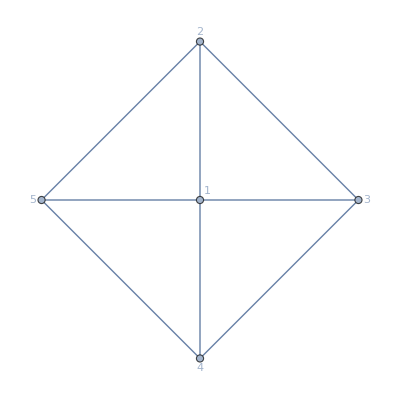

```mathematica
PlanarGraph[AdjacencyGraph[If[#==-1,1,0]&/@#&/@G1,VertexLabels->"Name"]]
```

Gluing them together, we get the gram matrix for the octahedron, like we would expect.

```mathematica
(G3=fullGlue[G1,G2,4])//MatrixForm
```

(1 | -1 | -1 | -1 | -1 | -3
-1 | 1 | -1 | -3 | -1 | -1
-1 | -1 | 1 | -1 | -3 | -1
-1 | -3 | -1 | 1 | -1 | -1
-1 | -1 | -3 | -1 | 1 | -1
-3 | -1 | -1 | -1 | -1 | 1)

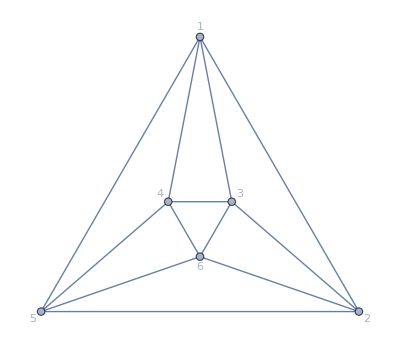

```mathematica
PlanarGraph[AdjacencyGraph[If[#==-1,1,0]&/@#&/@G3,VertexLabels->"Name"]]
```